## Defining Functions

```mathematica
1/3
```

1/3

```mathematica
myRandom:=RandomInteger[10]
```

```mathematica
MyAdd[x_]:=3+x
```

```mathematica
MyAdd[x_,y_]:=3+x*y
```

```mathematica
Information@MyAdd
```

```mathematica
MyAdd[9,5]
```

48

```mathematica
Fn01[x_Integer]:=5x
```

```mathematica
Fn01[x_Rational]:=3x
```

```mathematica
Fn01[x_Real/;x>0]:=0.1x
Fn01[x_Real/;x<=0]:=0.01x
```

```mathematica
Information@Fn01
```

```mathematica
Fn01[7]
```

35

```mathematica
Fn01[5/2]
```

15/2

```mathematica
Fn01[-0.5]
```

-0.005

```mathematica
ImageDimensions@-Graphics-
```

```mathematica
{218,128}
img01 = -Graphics-
```

{218,128}

-Graphics-

```mathematica
Fn02[img_Image]:=ImagePartition[img,32]
```

```mathematica
Fn02[img01]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Information@Fn02
```

```mathematica
Clear@Fn02
```

```mathematica
MyPartition[img_Image,n_Integer]:=ImagePartition[img,Round[ImageDimensions@img/n]]
```

```mathematica
MyPartition[img01,3]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Partition[Table[1,16],4]
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

```mathematica
MyPartition[list_List,n_Integer]:=Partition[list,n]
```

```mathematica
Information@MyPartition
```

## More About Patterns

```mathematica
Cases[{1,2,3,4.45,5/3,"dsd",6},_String]
```

{dsd}

```mathematica
Cases[{1,2,3,{3,3,2.0},4.45,5/3,"dsd",6},_Real,All]
```

{2.,4.45}

```mathematica
Cases[{1,2,3,{3,3,2.0},4.45,5/3,"dsd",6},_Real,{2}]
```

{2.}

```mathematica
Cases[{1,2,3,{3,3,2.0},4.45,5/3,"dsd",6},x_Real/;x>4:>x+1,All]
```

{5.45}

```mathematica
Replace[{1,2,3,{3,3,2.0},4.45,5/3,"dsd",6},x_Real/;x>4:>x+1,All]
```

{1,2,3,{3,3,2.},5.45,5/3,dsd,6}

```mathematica
Position[{1,2,3,{3,3,2.0},4.45,5/3,"dsd",6},_Real,All]
```

{{4,3},{5}}

```mathematica
Count[{1,2,3,{3,3,2.0},4.45,5/3,"dsd",6},_Real,All]
```

2

```mathematica
fn=5+#&
```

5+#1&

```mathematica
fn[5]
```

10

```mathematica
Map[fn,{5,6,7}]
```

{10,11,12}

```mathematica
fn/@{7,7,8}
```

{12,12,13}

```mathematica
d1 = Range@12;
d2=Range@6;
coords=Tuples[{d1,d2}]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6}}

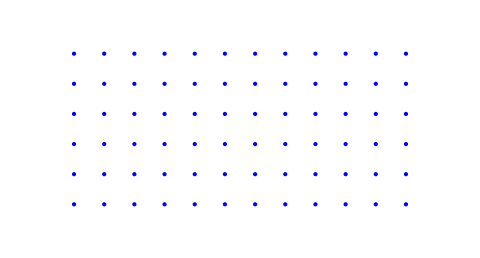

```mathematica
G1 = Graphics[{{Blue,Point@#}&/@coords},ImageSize->480,PlotRange->{{0,13},{0,7}}]
```

```mathematica
-Graphics-[[1,1]]
```

{RGBColor[0, 0, 1],Point[{1,1}]}

```mathematica
Cases[G1,Point[{3,_}],All]
```

{Point[{3,1}],Point[{3,2}],Point[{3,3}],Point[{3,4}],Point[{3,5}],Point[{3,6}]}

```mathematica
Cases[G1,Point[{3,y_}]:>y,All]
```

{1,2,3,4,5,6}

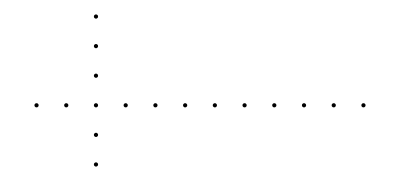

```mathematica
Graphics@Cases[G1,Point[{x_,y_}]/;3<=x<4||y==3,All]
```

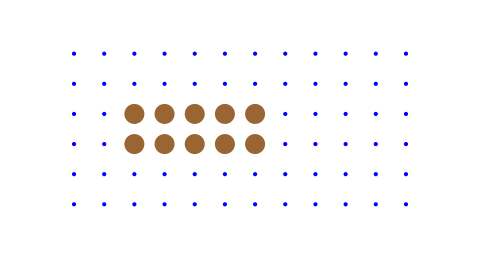

```mathematica
G2=Replace[G1,{___,Point[{x_,y_}]}/;2<x<8&&2<y<5:>{Brown,PointSize@.03,Point[{x,y}]},All
]
```

```mathematica
Count[G2,Red,All]
```

10

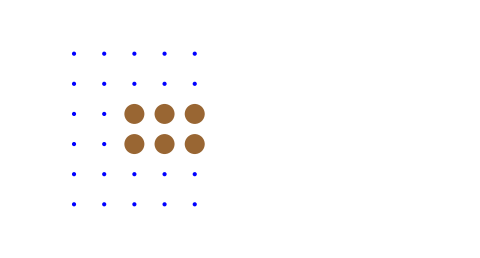

```mathematica
G3 = DeleteCases[G2,{___,Point[{x_,y_}],___}/;x>5,All]
```

```mathematica
G4 = Graphics3D[
Replace[G2[[1]],{
{Brown,___,Point[{x_,y_}]}:>{Red,Sphere[{x,y,0},.3]},
{}
}
,All]
,Boxed->False,Lighting->"Neutral"]
```

## Parser of wiki

```mathematica
url="https://en.wikipedia.org/wiki/Led_Zeppelin"
```

https://en.wikipedia.org/wiki/Led_Zeppelin

```mathematica
xml =Import[url,"XMLObject"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Standalone→yes]},XMLElement[html,{1},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],32,XMLElement[link,{rel→dns-prefetch,href→…g},{}]}],XMLElement[1]}],{}]
 |  |  |  |

```mathematica
title=Cases[
xml,
XMLElement["title",{},{a_}]:>a,
All
]
```

{Led Zeppelin - Wikipedia}

```mathematica
xml2=Replace[xml,XMLElement["b",{},a_]:>a,All]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Standalone→yes]},XMLElement[html,{1},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],32,XMLElement[link,{rel→dns-prefetch,href→…g},{}]}],XMLElement[1]}],{}]
 |  |  |  |

```mathematica
para1=Cases[
xm2,
XMLElement["p",{},a_]:>a,
All,1
]
```

{{{Led Zeppelin}, were  an English rock band formed in London in 1968. The group consisted of vocalist ,XMLElement[a,{shape→rect,href→/wiki/Robert_Plant,title→Robert Plant},{Robert Plant}],, guitarist ,XMLElement[a,{shape→rect,href→/wiki/Jimmy_Page,title→Jimmy Page},{Jimmy Page}],, bassist/keyboardist ,XMLElement[a,{shape→rect,href→/wiki/John_Paul_Jones_(musician),title→John Paul Jones (musician)},{John Paul Jones}],, and drummer ,XMLElement[a,{shape→rect,href→/wiki/John_Bonham,title→John Bonham},{John Bonham}],. With a heavy, guitar-driven sound, they are cited as one of the progenitors of ,XMLElement[a,{shape→rect,href→/wiki/Hard_rock,title→Hard rock},{hard rock}], and ,XMLElement[a,{shape→rect,href→/wiki/Heavy_metal_music,title→Heavy metal music},{heavy metal}],, although their style drew from a variety of influences, including ,XMLElement[a,{shape→rect,href→/wiki/Blues,title→Blues},{blues}], and ,XMLElement[a,{shape→rect,href→/wiki/Folk_music,title→Folk music},{folk music}],. Led Zeppelin have been credited as significantly impacting the nature of the music industry, particularly in the development of ,XMLElement[a,{shape→rect,href→/wiki/Album-oriented_rock,title→Album-oriented rock},{album-oriented rock}], (AOR) and ,XMLElement[a,{shape→rect,href→/wiki/Arena_rock,title→Arena rock},{stadium rock}],.
}}

```mathematica
links=Cases[
xml,
{"href"->a_}:>a,
All,12
]
```

{}

```mathematica
xml2=Cases[xml,XMLElement["img",_,_],All,12];
```

```mathematica
xml2[[1]]
```

XMLElement[img,{alt→This is a good article. Click here for more information.,src→//upload.wikimedia.org/wikipedia/en/thumb/9/94/Symbol_support_vote.svg/19px-Symbol_support_vote.svg.png,decoding→async,width→19,height→20,srcset→//upload.wikimedia.org/wikipedia/en/thumb/9/94/Symbol_support_vote.svg/29px-Symbol_support_vote.svg.png 1.5x, //upload.wikimedia.org/wikipedia/en/thumb/9/94/Symbol_support_vote.svg/39px-Symbol_support_vote.svg.png 2x,data-file-width→180,data-file-height→185},{}]

```mathematica
Cases[xml2,{"src"->a_}:>a,All]
```

{}

example

```mathematica
code = Cell["example","Text",CellChangeTimes->{{3.8740387925050488*^9,3.8740388366003733*^9}}]
CellPrint@code
```

Cell[example,Text,CellChangeTimes→{{3.87404×10^9,3.87404×10^9}}]

example